## Functional Programming Part 2

Hello and welcome to our second lecture on functional programming.

### Nest & NestList

Another set of very useful functions are the Nest and NestList functions:

```mathematica
?Nest
```

Nest[f,expr,n] gives an expression with f applied n times to expr.

We’ve seen that the Map function applies a function to every element in a list. It’s like an iterator over a sequence that transforms each element. Nest repeatedly applies a function to a single element n times. For the programmers, Nest is a convenient function for performing tail recursion a set number of times. For example, here we apply f to x 10 times:

```mathematica
Nest[f,x,10]
```

f[f[f[f[f[f[f[f[f[f[x]]]]]]]]]]

If f were a function that doubles x each time where x started at 1, then we could use Nest to compute the powers of two. Here’s the 10th power of 2 using Nest:

```mathematica
Nest[2#&,1,10]
```

1024

If you wanted all the powers of two in a list, we would use NestList:

```mathematica
?NestList
```

NestList[f,expr,n] gives a list of the results of applying f to expr 0 through n times.

```mathematica
NestList[2#&,1,10]
```

{1,2,4,8,16,32,64,128,256,512,1024}

We will see this used in a project in the next lecture.

### NestWhile & NestWhileList

In most recursion, the recursion ends when a terminating condition has been met. NestWhile and NestWhileList are variants of Nest and NestList that apply the recursion until a condition has been met. For the programmers, NestWhile is a convenient function for performing tail recursion. Let’s look at NestWhileList first:

```mathematica
?NestWhileList
```

NestWhileList[f,expr,test] generates a list of the results of applying f repeatedly, starting with expr, and continuing until applying test to the result no longer yields True. 
NestWhileList[f,expr,test,m] supplies the most recent m results as arguments for test at each step. 
NestWhileList[f,expr,test,All] supplies all results so far as arguments for test at each step. 
NestWhileList[f,expr,test,m,max] applies f at most max times.

Let’s use it to compute all powers of two less than a million:

```mathematica
NestWhileList[2#&,1,#<1000000&]
```

{1,2,4,8,16,32,64,128,256,512,1024,2048,4096,8192,16384,32768,65536,131072,262144,524288,1048576}

Here, we pass our doubling pure function as the first argument, and a test condition function as the last argument. When the test condition is no longer satisfied, the recursion ends.

A neat example of using NestWhile is to compute the greatest common divisor, or GCD, of two numbers. The GCD can be computed using Euclidean Algorithm, which states:

gcd(a,0)=a
gcd(a,b)=gcd(b,a mod b)

So, the GCD of 1071 and 462 is:

```mathematica
NestWhile[{#[[2]],Mod[#[[1]],#[[2]]]}&,{1071,462},#[[2]]≠0&]
```

{21,0}

And so, the gcd is 21.

Of course, you could have defined a gcd function as follows:

```mathematica
gcd[a_Integer,0]:=a
```

```mathematica
gcd[a_Integer,b_Integer]:=gcd[b,Mod[a,b]]
```

```mathematica
gcd[1071,462]
```

21

Using NestWhile is simply an alternative to formally defining the function. It’s up to you how you decide to implement your functions. One nice thing about our NestWhile implementation of the Euclidean Algorithm is, we can see the intermediate values of our computation by simply changing NestWhile to NestWhileList:

```mathematica
NestWhileList[{#[[2]],Mod[#[[1]],#[[2]]]}&,{1071,462},#[[2]]≠0&]
```

{{1071,462},{462,147},{147,21},{21,0}}

Neat, right?

### FixedPoint & FixedPointList

```mathematica
?FixedPoint
```

FixedPoint[f,expr] starts with expr, then applies f repeatedly until the result no longer changes.

```mathematica
?FixedPointList
```

FixedPointList[f,expr] generates a list giving the results of applying f repeatedly, starting with expr, until the results no longer change.

Newton’s method is an iterative procedure to find the roots or zeros of a function. It’s defined as follows:

x_(n+1)=x_n-(f(x_n))/(f'(x_n))

You start by giving it an initial guess (x_n), and it iterates until it finds the root.

Let’s say our function was x^2-1. This function has two roots, -1 and 1:

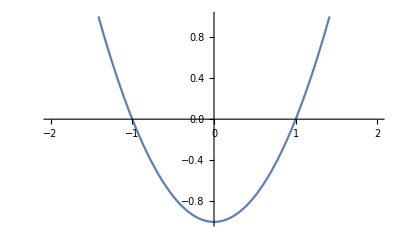

```mathematica
Plot[x^2-1,{x,-2,2},ImageSize->Tiny,PlotRange->{{-2,2},{-1,1}}]
```

Now we define Newton’s method.

```mathematica
Newton[xn_,f_,fp_]:=xn-f[xn]/fp[xn]
```

f is the function, and fp is the derivative of the function and xn is our initial guess.

```mathematica
FixedPointList[Newton[#,#^2-1&,2 #&]&,1.2]
```

{1.2,1.01667,1.00014,1.,1.,1.}

### Fold & FoldList

So, we’ve now seen how to iterate over list elements with Map and how to perform tail recursion with Nest. The last of the functional programming tools are Fold and FoldList.

```mathematica
?Fold
```

Fold[f,x,list] gives the last element of FoldList[f,x,list].
Fold[f,list] is equivalent to Fold[f,First[list],Rest[list]].

The Fold function applies a function f to the first two elements of a list, then re-applies f to the result, and the next element, and so on, recursively:

```mathematica
Fold[f,{a,b,c,d}]
```

f[f[f[a,b],c],d]

So in this case, we apply f to a and b. f is then applied to the result of the previous evaluation and c, and so on. If we wanted to add up all the values in a list, we could fold the Plus function over the list of values:

```mathematica
Fold[Plus,{a,b,c,d}]
```

a+b+c+d

FoldList does what you might expect:

```mathematica
?FoldList
```

FoldList[f,x,{a,b,…}] gives {x,f[x,a],f[f[x,a],b],…}. 
FoldList[f,{a,b,c,…}] gives {a,f[a,b],f[f[a,b],c],…}.

The first element in the list is a, the second is f of a, b, and so on. It’s basically each of the intermediate values that Fold computes before returning the final result:

```mathematica
FoldList[Plus,{a,b,c,d}]
```

{a,a+b,a+b+c,a+b+c+d}

Let’s use what we’ve learned to demonstrate the Law of Large numbers. The Law of Large numbers states that if you perform an experiment a large number of times, the average number obtained from performing the experiment converges to the expected value. Let’s say our experiment draws random numbers from a normal distribution.

In Mathematica, we use the NormalDistribution function to represent a normal distribution:

```mathematica
?NormalDistribution
```

NormalDistribution[μ,σ] represents a normal (Gaussian) distribution with mean μ and standard deviation σ.
NormalDistribution[] represents a normal distribution with zero mean and unit standard deviation.

We can draw random numbers from a distribution using the RandomVariate function:

```mathematica
?RandomVariate
```

RandomVariate[dist] gives a pseudorandom variate from the symbolic distribution dist.
RandomVariate[dist,n] gives a list of n pseudorandom variates from the symbolic distribution dist.
RandomVariate[dist,{n_1,n_2,…}] gives an n_1× n_2×… array of pseudorandom variates from the symbolic distribution dist.

Let’s generate some samples. Our normal distribution will have a mean of 85 and standard deviation of 5 and we will repeat the experiment 200 times:

```mathematica
samples=Table[RandomVariate[NormalDistribution[85,5]],{200}];
```

Since the expected value of a normal distribution is just the mean, we expect that the rolling average will converge to 85 as we consider more and more samples:

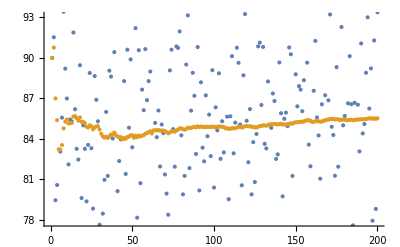

```mathematica
ListPlot[{
samples,
FoldList[Plus,samples]/Range[Length[samples]]
}]
```

Here, the blue dots are the samples, and the orange dots represent the running average and we can see that they converge to 85. Voila! Just as we, “expected”. ;)

### Summary

This concludes our lecture on functional programming. In this lecture, we covered some of the basic building blocks that Mathematica provides for doing functional programming. In many cases, you won’t need to use these functions because Mathematica provides other functions that are easier to reason about. That being said, it is important to be aware of the fundamentals. Thanks and see you at the next lecture!